```mathematica
Get["lqrw.m", Path -> {"f:\\MSc"}]
BitOrder=3;
σ=ⅇ^((π 2 ⅈ)/BitOrder);
({{a, b, c}, {d, e, f}, {g, h, i}})=H=({{1, 1, 1}, {1, σ^(BitOrder-1), σ}, {1, σ, σ^(BitOrder-1)}})/(√BitOrder);
Test=Normal[SparseArray[{
{1,1}->a1,
{1,2}->b1,
{1,3}->c1,
{2,1}->a2,
{2,2}->b2,
{2,3}->c2,
{3,1}->a3,
{3,2}->b3,
{3,3}->c3,
{4,1}->a4,
{4,2}->b4,
{4,3}->c4
}]];
Test = Normal[SparseArray[{
{4,3}->0,
{1,1}->1
}]]
FairClassicCoin=({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}})/2;
LazyClassicCoin=({{1, 1, 1}, {1, 1, 1}, {1, 1, 1}})/3;
HadamardCoin=({{0, 0, 0}, {0, 1, 1}, {0, 1, -1}})/Sqrt[2];
```

(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
StatesToPositionalProbabilites[SingleLazyItteration[Test,H]]
Simplify[StatesToPositionalProbabilites[MultipleLazySteps[Test,H,10]]]
```

```mathematica
QuantumLazyLine100Steps=
QuantumStatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{200,3}->0,
{100,1}->1
}]]
,H,100];
```

```mathematica
QuantumLine100Steps=
QuantumStatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{200,3}->0,
{100,2}->1/Sqrt[2],
{100,3}->I/Sqrt[2]
}]]
,HadamardCoin,100];
```

```mathematica
ClassicLine100Steps=
ClassicStatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{200,3}->0,
{100,2}->1/2,
{100,3}->1/2
}]]
,FairClassicCoin,100];
ClassicLazyLine100Steps=
ClassicStatesToPositionalProbabilites/@MultipleLazyStepsHistory[
Normal[SparseArray[{
{200,3}->0,
{100,1}->1
}]]
,LazyClassicCoin,100];
```

```mathematica
Table[ListPlot3D[g,
PlotRange->{0,0.15},
ImageSize->Large,
ViewPoint->{-.4,2,1},
ColorFunction->Hue,
Mesh->None
],
{g,{ClassicLine100Steps,ClassicLazyLine100Steps,QuantumLine100Steps,QuantumLazyLine100Steps}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

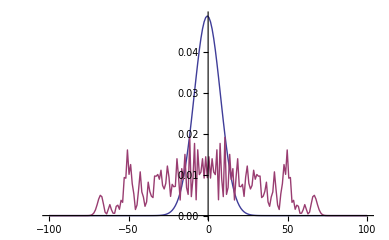

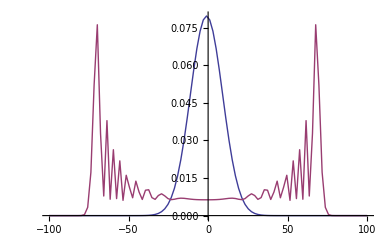

```mathematica
ListPlot[Table[Last[g],
{g,{ClassicLazyLine100Steps,QuantumLazyLine100Steps}}],
Joined->True,
PlotRange->All,
DataRange->{-100,100}
]
ListPlot[Table[Last[g][[2;;200;;2]],
{g,{ClassicLine100Steps,QuantumLine100Steps}}],
Joined->True,
PlotRange->All,
DataRange->{-100,100}
]
```

```mathematica
Clear[com];
re=Re[com];im=Im[com];
(re+im*I)*Conjugate[(re+im*I)]
```

(Re(com)-ⅈ Im(com)) (Re(com)+ⅈ Im(com))

```mathematica
ReTheta=Re[Th];
Normal[Simplify[StatesToPositionalProbabilites[SparseArray[{
{4,3}->0,
{2,2}->(1/Sqrt[2])+ReTheta*I,
{2,3}->(1/Sqrt[2])+Sqrt[-(ReTheta^2)]*I
}]]]]
```

{0,-√2 Abs[Re(Th)]+2 (Re(Th))^2+1,0,0}

```mathematica
Simplify[Sqrt[-(cc^2)]]
```

√(-cc^2)

```mathematica
Transpose[Table[N[Take[UpTo10Nodes100Steps[[v]],-1]],{v,Range[10]}]]
```

({1.} | {0.499806,0.500194} | {0.44,0.28,0.28} | {0.295065,0.195167,0.314601,0.195167} | {0.279799,0.184843,0.175257,0.175257,0.184843} | {0.219524,0.136209,0.138299,0.23146,0.138299,0.136209} | {0.216387,0.144407,0.121052,0.126348,0.126348,0.121052,0.144407} | {0.164854,0.109312,0.101085,0.114226,0.185901,0.114226,0.101085,0.109312} | {0.15735,0.108814,0.0977045,0.10262,0.112186,0.112186,0.10262,0.0977045,0.108814} | {0.134377,0.0889039,0.0804857,0.0858994,0.0994989,0.156047,0.0994989,0.0858994,0.0804857,0.0889039})

```mathematica
UpTo16Nodes2000Steps>>"F:\MSc\UpTo16Nodes2000Steps.txt"
```

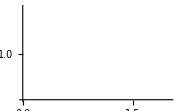
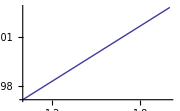
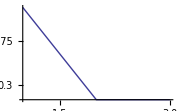
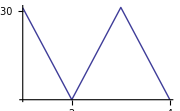
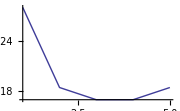
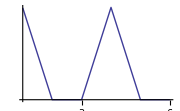
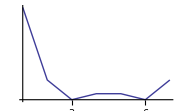
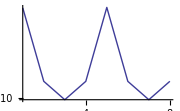

```mathematica
Table[
ListLogPlot[Mean/@Transpose[
Take[
UpTo16Nodes2000Steps[[v]],
-500
]],
ImageSize->Small,
PlotRange->All,
Joined->True
],
{v, Range[16]}]
```